```mathematica
Quit[]
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
Rn[n_,s2_]=Simplify[Sqrt[3 σn2[n,s2]/σn2[n+1,s2]],{s2>0,n>0,ks>0}]
```

(√3 ⅇ^(-((1+2 n) s2)))/ks

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2]
3 γn[s2]^4
```

3 ⅇ^(-8 s2)

3 ⅇ^(-8 s2)

```mathematica
CC={{C11,C12,C13},{C12,C22,C23},{C13,C23,C33}};
Cp={{C22,C23},{C23,C33}};
```

```mathematica
P1[X1_,X2_,X3_]=1/Sqrt[(2π)^3 Abs[Det[CC]]] Exp[-1/2{X1,X2,X3}.Inverse[CC].{X1,X2,X3}]//Simplify
```

(ⅇ^(-(C23^2 X1^2+2 C12 C33 X1 X2+C13^2 X2^2-C11 C33 X2^2-2 C12 C13 X2 X3+C12^2 X3^2-2 C23 (C13 X1 X2+C12 X1 X3-C11 X2 X3)-C22 (C33 X1^2-2 C13 X1 X3+C11 X3^2))/(2 (C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)))))/(2 √2 π^(3/2) √Abs[C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)])

```mathematica
Integrate[P1[X1,X2,X3],{X1,-∞,∞},Assumptions->{C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0,C23^2-C22 C33>0}]//Simplify
```

(ⅇ^((C33 X2^2-2 C23 X2 X3+C22 X3^2)/(2 C23^2-2 C22 C33)))/(2 √((C23^2-C22 C33)/(C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33)) π √Abs[C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)])

```mathematica
P1p[X2_,X3_]=1/Sqrt[(2π)^2 Abs[Det[Cp]]] Exp[-1/2{X2,X3}.Inverse[Cp].{X2,X3}]//Simplify
```

(ⅇ^((C33 X2^2-2 C23 X2 X3+C22 X3^2)/(2 C23^2-2 C22 C33)))/(2 π √Abs[C23^2-C22 C33])

```mathematica
P1[z,m2,-m2 k3^2]/P1p[m2,-m2 k3^2]//Simplify
```

(ⅇ^(-((C13 (C23+C22 k3^2) m2-C12 (C33+C23 k3^2) m2-C23^2 z+C22 C33 z)^2)/(2 (C23^2-C22 C33) (C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)))) √Abs[C23^2-C22 C33])/(√(2 π) √Abs[C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)])

```mathematica
meanz=FullSimplify[1/P1p[m2,-m2 k3^2] Integrate[z P1[z,m2,-m2 k3^2],{z,-∞,∞},Assumptions->{C23^2-C22 C33>0,C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0}],{C23^2-C22 C33>0,C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0}]
```

((C13 (C23+C22 k3^2)-C12 (C33+C23 k3^2)) m2)/((C23^2-C22 C33) √(1/Sign[C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33]))

```mathematica
meanzSim=Collect[Simplify[Simplify[meanz/.{Sign[C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33]->1}]/.{C12->σ1^2 ψ1,C13->-σ2^2 ψ2,C22->σ2^2,C33->σ4^2,C23->-σ3^2,m2->σ2^2/σ1^2 m2t,k3^2->σ4/σ2 k3t^2}],{ψ1,ψ2}]
```

-(m2t σ2 (-k3t^2 σ1^2 σ3^2 σ4+σ1^2 σ2 σ4^2) ψ1)/(σ1^2 (σ3^4-σ2^2 σ4^2))-(m2t σ2 (-σ2^3 σ3^2+k3t^2 σ2^4 σ4) ψ2)/(σ1^2 (σ3^4-σ2^2 σ4^2))

```mathematica
Collect[Simplify[m2t(1/(1-γ3^2)(ψ1-1/3 R3^2 σ2^2/σ1^2 ψ2)-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1-1/3 R3^2 σ2^2/σ1^2 ψ2))-meanzSim/.{γ3->σ3^2/(σ2 σ4),R3->Sqrt[3] σ3/σ4}],{ψ1,ψ2}]
```

0

```mathematica
Collect[(meanzSim(1-γ3^2))/(σ0 ν2 γ1)/.{σ3^2->γ3 σ2 σ4,σ3^4->(γ3 σ2 σ4)^2,m2t->ν2 σ1^2/σ2,γ1->σ1^2/(σ0 σ2)},{ψ1,ψ2},Simplify]/.{σ4->σ3^2/(γ3 σ2)}/.{1/σ1^2->(σ2^4/(γ2^2 σ3^2))^-1}
```

(1-k3t^2 γ3) ψ1+γ2^2 (k3t^2-γ3) γ3 ψ2

```mathematica
varz=FullSimplify[1/P1p[m2,-m2 k3^2] Integrate[z^2 P1[z,m2,-m2 k3^2],{z,-∞,∞},Assumptions->{C23^2-C22 C33>0,C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0}],{C23^2-C22 C33>0,C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0}]
```

((C23^2-C22 C33) (C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33))+(C13 (C23+C22 k3^2)-C12 (C33+C23 k3^2))^2 m2^2)/((C23^2-C22 C33)^2 √(1/Sign[C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33]))

```mathematica
varzSim=FullSimplify[varz,{C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33)>0,C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33>0}]/.{Sign[C13^2 C22-2 C12 C13 C23+C11 C23^2+C12^2 C33-C11 C22 C33]->1}
```

((C23^2-C22 C33) (C13^2 C22-2 C12 C13 C23+C12^2 C33+C11 (C23^2-C22 C33))+(C13 (C23+C22 k3^2)-C12 (C33+C23 k3^2))^2 m2^2)/((C23^2-C22 C33)^2)

```mathematica
varzCol=Collect[FullSimplify[FullSimplify[varzSim/σ0^2/.{C11->σ0^2,C12->σ1^2 ψ1,C13->-σ2^2 ψ2,C22->σ2^2,C33->σ4^2,C23->-σ3^2(*,m2->σ2^2/σ1^2 m2t*),m2->ν2 σ2,k3^2->σ4/σ2 k3t^2}/.{ψ2->(σ1^2 σ3^2)/σ2^4(σ2^2 σ4^2)/σ3^4 g3g2ψ2}]/.{σ3^2->γ3 σ2 σ4,σ3^4->(γ3 σ2 σ4)^2,σ3^8->(γ3 σ2 σ4)^4,1/σ3^4->1/(γ3 σ2 σ4)^2}]/.{σ3^2->γ3 σ2 σ4,1/σ3^4->1/(γ3 σ2 σ4)^2,σ1^4->γ1^2 σ0^2 σ2^2,g3g2ψ2->γ3^2 γ2^2 ψ2},{ψ1,ψ2},Simplify]
```

1+(γ1^2 (-1+γ3^2+(-1+k3t^2 γ3)^2 ν2^2) ψ1^2)/((-1+γ3^2)^2)+(2 γ1^2 γ2^2 γ3 (γ3-γ3^3+(-k3t^2+γ3) (-1+k3t^2 γ3) ν2^2) ψ1 ψ2)/((-1+γ3^2)^2)+(γ1^2 γ2^4 γ3^2 (-1+γ3^2+(k3t^2-γ3)^2 ν2^2) ψ2^2)/((-1+γ3^2)^2)

```mathematica
C2={{Cxx,Cxy,Cx2,Cx4},{Cxy,Cyy,Cy2,Cy4},{Cx2,Cy2,C22,C24},{Cx4,Cy4,C24,C44}};
```

```mathematica
P12[Xx_,Xy_,X2_,X4_]=1/Sqrt[(2π)^4 Abs[Det[C2]]] Exp[-1/2{Xx,Xy,X2,X4}.Inverse[C2].{Xx,Xy,X2,X4}];
```

```mathematica
Integrate[Sin[k ρ]/ρ(Sin[k r]-k r Cos[k r])/r,{k,0,∞}]
```

Integrate::idiv: Integral of -(k Cos[k r] Sin[k ρ])/ρ+(Sin[k r] Sin[k ρ])/(r ρ) does not converge on {0,∞}.

∫_0^∞ ((-k r Cos[k r]+Sin[k r]) Sin[k ρ])/(r ρ)ⅆk

```mathematica
Simplify[(π ((r-ρ)/(√((r-ρ)^2))+(r+ρ)/(√((r+ρ)^2))))/(4 r),{r>ρ,r+ρ>0}]
Simplify[(π ((r-ρ)/(√((r-ρ)^2))+(r+ρ)/(√((r+ρ)^2))))/(4 r),{ρ>r,r+ρ>0}]
```

π/(2 r)

0

```mathematica
Integrate[Sinc[k rp],{rp,0,r}]
```

SinIntegral[k r]/k

```mathematica
Integrate[rp^2 Sinc[k rp],{rp,0,r}]
```

(-k r Cos[k r]+Sin[k r])/k^3

```mathematica
Integrate[rp^2 Sinc[k rp]Sinc[q rp],{rp,0,r}]
```

(q Cos[q r] Sin[k r]-k Cos[k r] Sin[q r])/(k^3 q-k q^3)

```mathematica
Integrate[r^2 Sinc[k r]Sinc[q r],{r,0,∞}]
```

Integrate::idiv: Integral of r^2 Sinc[k r] Sinc[q r] does not converge on {0,∞}.

∫_0^∞ r^2 Sinc[k r] Sinc[q r]ⅆr

```mathematica
WRTH[z_]=(3(Sin[z]-z Cos[z]))/z^3;
```

```mathematica
WRTH[z]^2//FullSimplify
```

(9 (-z Cos[z]+Sin[z])^2)/z^6

```mathematica
Integrate[k^4 WRTH[k r](q Cos[q r] Sin[k r]-k Cos[k r] Sin[q r])/(k^3 q-k q^3)//TrigExpand,{k,0,∞}]
```

$Aborted

```mathematica
k^4 WRTH[k r](q Cos[q r] Sin[k r]-k Cos[k r] Sin[q r])/(k^3 q-k q^3)//FullSimplify
```

(3 (k r Cos[k r]-Sin[k r]) (q Cos[q r] Sin[k r]-k Cos[k r] Sin[q r]))/((-k^2 q+q^3) r^3)

### monochromatic

```mathematica
Quit[]
```

```mathematica
CC={{C11,C12},{C12,C22}}/.{C11->As,C12->As ks^2 Sinc[ks r],C22->As ks^4};
```

```mathematica
P1[X1_,X2_]=Simplify[1/Sqrt[(2π)^2 Abs[Det[CC]]] Exp[-1/2{X1,X2}.Inverse[CC].{X1,X2}],{As^2 ks^4(1-Sinc[ks r]^2)>0,As>0}]
P1p[X2_]=Simplify[1/Sqrt[2π C22] Exp[-1/2 X2^2/C22]/.{C22->As ks^4},{ks>0}]
```

(ⅇ^((ks^4 X1^2+X2^2-2 ks^2 X1 X2 Sinc[ks r])/(2 As ks^4 (-1+Sinc[ks r]^2))))/(2 As ks^2 π √(1-Sinc[ks r]^2))

(ⅇ^(-X2^2/(2 As ks^4)))/(√As ks^2 √(2 π))

```mathematica
meanz[r_]=1/P1p[m2] Integrate[z P1[z,m2],{z,-∞,∞},Assumptions->{As>0,1-Sinc[ks r]^2>0}]
```

(m2 Sinc[ks r])/ks^2

```mathematica
varz[r_]=1/P1p[m2] Integrate[z^2 P1[z,m2],{z,-∞,∞},Assumptions->{As>0,1-Sinc[ks r]^2>0}]
```

(As ks^4+(-As ks^4+m2^2) Sinc[ks r]^2)/ks^4

```mathematica
varz[r_]//Simplify
```

As+(-As+m2^2/ks^4) Sinc[ks r_]^2

```mathematica
sd[r_]=Simplify[Sqrt[varz[r]-meanz[r]^2]]
```

√(As-As Sinc[ks r]^2)

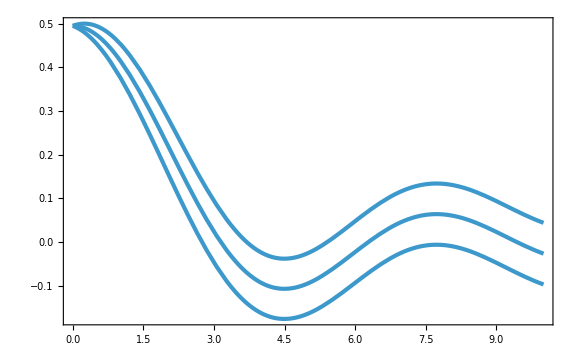

```mathematica
Plot[{meanz[r],meanz[r]+sd[r],meanz[r]-sd[r]}/.{As->5 10^-3,m2->7 Sqrt[5 10^-3],ks->1},{r,0,10}]
```

```mathematica
meanC[r_]=4/3 1/r Integrate[rp^2 meanz[r],{rp,0,r}](*+2/3 1/r Integrate[rp^2 varz[r],{rp,0,r}]*)//Simplify
```

(4 m2 r^2 Sinc[ks r])/(9 ks^2)

```mathematica
typicalC[r_]=2/3(1-(1+r meanz'[r])^2)//Simplify
```

2/3 (1-((ks^3 r+ks m2 r Cos[ks r]-m2 Sin[ks r])^2)/(ks^6 r^2))

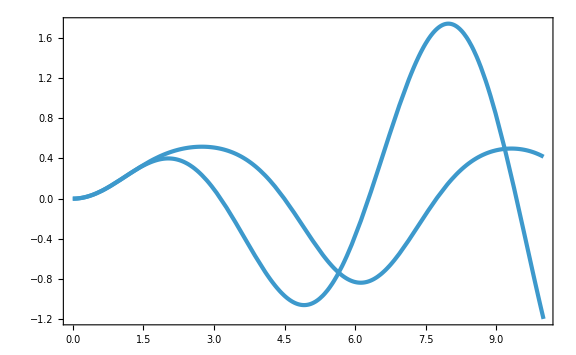

```mathematica
Plot[{meanC[r],typicalC[r]}/.{As->5 10^-3,m2->7 Sqrt[5 10^-3],ks->1},{r,0,10}]
```